Tue 10 Apr 2018

## Initialization

```mathematica
If[!TrueQ@LoadQ@#,
Import[
Last@
FileNames[
FileNameJoin@{
If[DirectoryStack[]=={},
NotebookDirectory[],Directory[]
],
#<>"_*.nb"
}]
,"Initialization"]
]&@
"Generator_Basis";

ClearAll[
TriggerFromSignal,SampleFromSignal
]

LoadQ["Generator_AWG_Basis"]=True;
```

## Variables

```mathematica
(* rate_Real = sampling rate of AWG *)
(* trigger_Real = trigger time of AWG *)
(* resolution_Integer = resolution of sample *)
(* default_Integer = default value of sample *)
(* sample: {___Integer} = sampling points of digital signal *)
```

## Functions

## Signal

```mathematica
TriggerFromSignal[{{
∞,t0_Real,
t1_Real
},
{∞,_Real,_Real}...
}]:=
t0;
TriggerFromSignal[signal_]:=0.

SampleFromSignal[
signal:{{
Except@_List,
_Real,_Real
}..
},{
rate_Real,
trigger_Real
},{
resolution_Integer,
default_Integer
}]:=Module[{
t1=⌈rate trigger⌉,
sample={},
sig,t0,t
},
Do[
t0=⌈rate sig⟦2⟧⌉;
If[t0>t1,
sample=
Join[
sample,Table[default,t0-t1]
],
t0=t1
];
t1=⌈rate sig⟦3⟧⌉;
If[t1>t0,
sig=
Compile[
{{t,_Integer}},
Evaluate[
default+
Round[
resolution(
First@sig/.
"t"->t/rate
)]]];
sample=
Join[
sample,
Table[
sig@t
,{t,t0,t1-1}]
],
t1=t0
],{sig,signal}];
sample
];
SampleFromSignal[
signal_,
{rate_Real,
trigger_Real
},{
resolution_Integer,
default_Integer
}]:=
{};
```

#### Examples

```mathematica
TriggerFromSignal@({{∞, 0., 0.03125}, {∞, 0.046875, 0.0625}})
TriggerFromSignal[
Cos[448.π"t"]
Sin[2."t"]^2
]
```

0.

0.

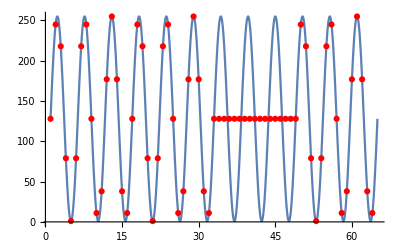

{}

```mathematica
Show[
Plot[
128+127Sin[0.375π(t-1)]
,{t,1,65}],
ListPlot[
SampleFromSignal[
({{Sin[384.π"t"], 0., 0.03125}, {Sin[384.π"t"], 0.046875, 0.0625}}),
{1024.,0.},
{127,128}
],PlotStyle->Red]
]
SampleFromSignal[
Cos[448.π"t"]
Sin[2."t"]^2,
{1024.,0.},
{127,128}
]
```